```mathematica
SetDirectory["C:\\Users\\kate\\Desktop\\LAB5\\lab5_1\\Files\\"];
```

```mathematica
Zero={{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}};
(*Setka=Join[Import["Diagramma.txt","Table"][[1;;-1,{1,2}]],Zero, 2]*)
Setka=Import["Diagramma4Test.txt","Table"][[1;;]]
```

```mathematica
iterData=Setka;
n = Length@iterData;
(*h = {Setka[[1]][[1]] - Setka[[2]][[1]], Setka[[1]][[2]] - Setka[[2]][[2]]}*)
```

```mathematica
h = {0.2, 0.2}
```

{0.2,0.2}

```mathematica
(*Grph=ListPlot3D[Setka, PlotRange->All,ColorFunction->Function[{#},Hue[Iter[[#]]]]][]*)
```

Функция цветов ячеек диаграммы

```mathematica
chooseColor[val_, a_, b_]:=Piecewise[{{White,val<=a},{Gray,a<val<=b}, {Black, b <val}}]
```

Функция создания ячейки

```mathematica
сolorBounds = {6, 7};
makeRec[data_List, k_]:={
EdgeForm[Thick],
chooseColor[data[[k]][[3]], сolorBounds[[1]], сolorBounds[[2]]],
Rectangle[
{data[[k]][[1]] - h[[1]]/2, data[[k]][[2]] - h[[2]]/2},
{data[[k]][[1]] + h[[1]]/2, data[[k]][[2]] + h[[2]]/2}
]
}
```

```mathematica
grid = Graphics[Table[makeRec[iterData, k], {k, 1, n}]];
```

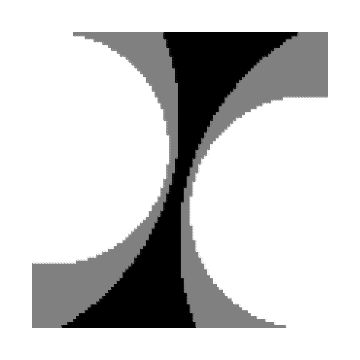

```mathematica
g =Show[grid,AspectRatio->1, ImageSize->Medium]
```

```mathematica
Export["test4.pdf",g]
```

test4.pdf